## Seasonal Ricker model - EWS in rb - Intervals

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tb460/Google\ Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_seasonal2"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=0;
bh=2.24;
```

## Import Data

```mathematica
(* Name of simluation run *)
simName="ricker_trans_rb_temp";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import["data_export/"<>simName<>"/ews_singles.csv"];
```

```mathematica
(* Import power spectrum DataFrame *)
dfPspec=Import["data_export/"<>simName<>"/pspec.csv"];
```

```mathematica
(* Import ews means DataFrame *)
dfEwsMeans=Import["data_export/"<>simName<>"/ews_means.csv"];
```

```mathematica
(* Import ews sd DataFrame *)
dfEwsSd=Import["data_export/"<>simName<>"/ews_deviations.csv"];
```

```mathematica
(* Import Kendall tau values *)
dfKtau=Import["data_export/"<>simName<>"/ktau.csv"];
```

```mathematica
numSims=Length[Union[dfEws[[2;;,1]]]]
```

3

```mathematica
(* Realisation number to display *)
displayNum=3;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* Extract info *)
realNum=1;
seriesB = Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Breeding",_,_}][[;;,{3,4}]];
seriesNB = Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Non-breeding",_,_}][[;;,{3,4}]];
seriesTotal= Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Total",_,_}][[;;,{3,4}]];
```

```mathematica
(* Useful info *)
tVals=seriesB[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
realMax=Max[dfEws[[;;,1]]][[1]];
stateVals=Union[dfEws[[2;;,2]]];
```

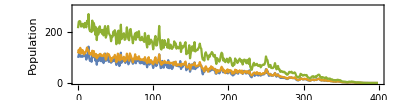

```mathematica
(* plot of breeding series *)
plotPop = ListPlot[{seriesB,seriesNB,seriesTotal},
Joined->True,
LabelStyle->12,
PlotLegends->Placed[trajLegend,Scaled[{0.85,0.7}]],
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Breeding growth rate, r_b"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
AxesLabel->{"t","Population"},
PlotRange->{{0,tmax},{0,300}}]
```

```mathematica
(* line legend *)
trajLegend=LineLegend[TMBcolours[[1;;3]],{"Breeding","Non-breeding","Total"},Spacings->{0,0.2},LabelStyle->10]
```

### Output

```mathematica
rTicks=Range[bl,bh,0.5];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

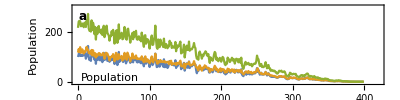

```mathematica
plotTraj=Show[{plotPop},
PlotRange->{{0,tmax*1.05},{-5,300}},
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Breeding growth rate, r_b"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}]}
]
```

## EWS Plots (Mean +/- SD)

### Variance

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEwsMeans[[1]],"Variance"][[1,1]];
```

```mathematica
dfEwsMeans[[1]]
```

{Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* mean of EWS *)
ewsMean=Table[
DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* standard deviation of EWS *)
ewsSd=Table[
DeleteCases[
Cases[dfEwsSd[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* time values *)
timeVals=DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{"Total",_,_}][[;;,{2,3}]],
{_,""}][[;;,1]];
```

```mathematica
plotB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[1]]-ewsSd[[1]],ewsMean[[1]],ewsMean[[1]]+ewsSd[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotNB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[2]]-ewsSd[[2]],ewsMean[[2]],ewsMean[[2]]+ewsSd[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotTot=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[3]]-ewsSd[[3]],ewsMean[[3]],ewsMean[[3]]+ewsSd[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

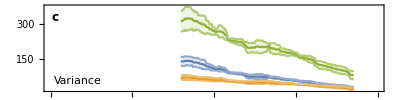

```mathematica
(* Plot EWS *)
plotVar=Show[{plotB,plotNB,plotTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}]
```

### Skewness

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEwsMeans[[1]],"Skewness"][[1,1]];
```

```mathematica
(* mean of EWS *)
ewsMean=Table[
DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* standard deviation of EWS *)
ewsSd=Table[
DeleteCases[
Cases[dfEwsSd[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* time values *)
timeVals=DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{"Total",_,_}][[;;,{2,3}]],
{_,""}][[;;,1]];
```

```mathematica
plotB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[1]]-ewsSd[[1]],ewsMean[[1]],ewsMean[[1]]+ewsSd[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotNB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[2]]-ewsSd[[2]],ewsMean[[2]],ewsMean[[2]]+ewsSd[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotTot=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[3]]-ewsSd[[3]],ewsMean[[3]],ewsMean[[3]]+ewsSd[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

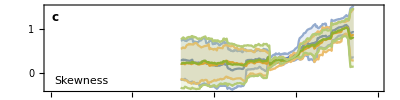

```mathematica
(* Plot EWS *)
plotSkew=Show[{plotB,plotNB,plotTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Skewness",ls],textPos,{-1,0}]}]
```

### Coefficient of variation

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEwsMeans[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
(* mean of EWS *)
ewsMean=Table[
DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* standard deviation of EWS *)
ewsSd=Table[
DeleteCases[
Cases[dfEwsSd[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* time values *)
timeVals=DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{"Total",_,_}][[;;,{2,3}]],
{_,""}][[;;,1]];
```

```mathematica
plotB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[1]]-ewsSd[[1]],ewsMean[[1]],ewsMean[[1]]+ewsSd[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotNB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[2]]-ewsSd[[2]],ewsMean[[2]],ewsMean[[2]]+ewsSd[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotTot=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[3]]-ewsSd[[3]],ewsMean[[3]],ewsMean[[3]]+ewsSd[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

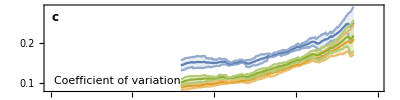

```mathematica
(* Plot EWS *)
plotCv=Show[{plotB,plotNB,plotTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

### Smax

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEwsMeans[[1]],"Smax"][[1,1]];
```

```mathematica
(* mean of EWS *)
ewsMean=Table[
DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* standard deviation of EWS *)
ewsSd=Table[
DeleteCases[
Cases[dfEwsSd[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* time values *)
timeVals=DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{"Total",_,_}][[;;,{2,3}]],
{_,""}][[;;,1]];
```

```mathematica
plotB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[1]]-ewsSd[[1]],ewsMean[[1]],ewsMean[[1]]+ewsSd[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotNB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[2]]-ewsSd[[2]],ewsMean[[2]],ewsMean[[2]]+ewsSd[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotTot=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[3]]-ewsSd[[3]],ewsMean[[3]],ewsMean[[3]]+ewsSd[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

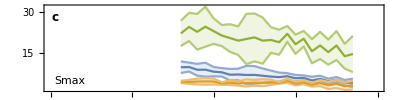

```mathematica
(* Plot variance EWS for display param *)
plotSmax=Show[{plotB,plotNB,plotTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Smax",ls],textPos,{-1,0}]}]
```

### Smax/Var

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEwsMeans[[1]],"Smax/Var"][[1,1]];
```

```mathematica
(* mean of EWS *)
ewsMean=Table[
DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* standard deviation of EWS *)
ewsSd=Table[
DeleteCases[
Cases[dfEwsSd[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* time values *)
timeVals=DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{"Total",_,_}][[;;,{2,3}]],
{_,""}][[;;,1]];
```

```mathematica
plotB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[1]]-ewsSd[[1]],ewsMean[[1]],ewsMean[[1]]+ewsSd[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotNB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[2]]-ewsSd[[2]],ewsMean[[2]],ewsMean[[2]]+ewsSd[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotTot=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[3]]-ewsSd[[3]],ewsMean[[3]],ewsMean[[3]]+ewsSd[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

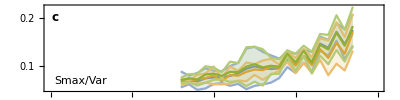

```mathematica
(* Plot EWS *)
plotSmaxVar=Show[{plotB,plotNB,plotTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Smax/Var",ls],textPos,{-1,0}]}]
```

### Lag-1 AC

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEwsMeans[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
(* mean of EWS *)
ewsMean=Table[
DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* standard deviation of EWS *)
ewsSd=Table[
DeleteCases[
Cases[dfEwsSd[[2;;,{1,2,indexEws}]],{state,_,_}][[;;,3]],
""],{state,stateVals}];
```

```mathematica
(* time values *)
timeVals=DeleteCases[
Cases[dfEwsMeans[[2;;,{1,2,indexEws}]],{"Total",_,_}][[;;,{2,3}]],
{_,""}][[;;,1]];
```

```mathematica
plotB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[1]]-ewsSd[[1]],ewsMean[[1]],ewsMean[[1]]+ewsSd[[1]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[1]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotNB=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[2]]-ewsSd[[2]],ewsMean[[2]],ewsMean[[2]]+ewsSd[[2]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[2]],
Filling->{1->{2},3->{2}}];
```

```mathematica
plotTot=ListLinePlot[Transpose[{timeVals,#}]&/@{ewsMean[[3]]-ewsSd[[3]],ewsMean[[3]],ewsMean[[3]]+ewsSd[[3]]},
PlotStyle->{Lighter[#],#,Lighter[#]}&@TMBcolours[[3]],
Filling->{1->{2},3->{2}}];
```

```mathematica
(* Y axis limits *)
ymin=-0.02;
ymax=0.3;
```

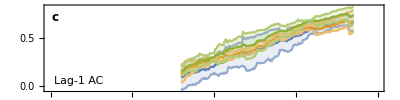

```mathematica
(* Plot EWS *)
plotAc1=Show[{plotB,plotNB,plotTot},
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
Filling->{{3->{1},3->{2}}},
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-1 AC",ls],textPos,{-1,0}]}]
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

### Variance

```mathematica
indexKtau=Position[dfKtau[[1]],"Variance"][[1,1]]
```

9

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.96906 | -0.970223 | -0.913887
Non-breeding | -0.922382 | -0.941429 | -0.871054
Total | -0.953233 | -0.948314 | -0.867388

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Skewness

```mathematica
indexKtau=Position[dfKtau[[1]],"Skewness"][[1,1]]
```

6

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.311365 | 0.246445 | 0.765895
Non-breeding | 0.320397 | 0.147724 | 0.874363
Total | 0.412769 | 0.0575874 | 0.915676

```mathematica
(* Box plot *)
boxSkew=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Coefficient of variation

```mathematica
indexKtau=Position[dfKtau[[1]],"Coefficient of variation"][[1,1]]
```

8

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.928195 | 0.651882 | 0.725118
Non-breeding | 0.954842 | 0.937763 | 0.985156
Total | 0.953948 | 0.867477 | 0.958508

```mathematica
(* Box plot *)
boxCv=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax"][[1,1]]
```

4

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.82684 | -0.844156 | -0.341991
Non-breeding | -0.61039 | -0.593074 | 0.411255
Total | -0.688312 | -0.69697 | 0.367965

```mathematica
(* Box plot *)
boxSmax=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Var

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax/Var"][[1,1]]
```

7

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.428571 | 0.645022 | 0.887446
Non-breeding | 0.619048 | 0.636364 | 0.82684
Total | 0.558442 | 0.61039 | 0.852814

```mathematica
(* Box plot *)
boxSmaxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-1 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-1 AC"][[1,1]]
```

10

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.924975 | 0.877582 | 0.950639
Non-breeding | 0.917196 | 0.875347 | 0.941429
Total | 0.950997 | 0.893141 | 0.940356

```mathematica
(* Box plot *)
boxAc1=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

## Power Spectrum Plot

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Organise power spectrum data

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[dfPspec[[2;;,3]]][[1;;-1;;8]]
```

{159.,239.,319.}

```mathematica
dfPspec[[1]]
```

{Realisation number,Variable,Time,Frequency,Empirical}

```mathematica
(* Power spectra of display plot *)
specData=Table[
Cases[dfPspec,{displayNum,"Total",timeVal,_,_}][[;;,{4,5}]],
{timeVal,plotTimes}];
```

```mathematica
(* Power spectra normalised by the variance *)
varianceVals=Table[Cases[dfEws[[2;;,{1,2,3,8}]],{displayNum,"Total",Round[time],_}][[1,4]],{time,plotTimes}];
specNormData=specData;
specNormData[[;;,;;,2]]=specNormData[[;;,;;,2]]/varianceVals;
```

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

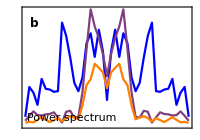

```mathematica
plotPspec=ListLinePlot[specData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

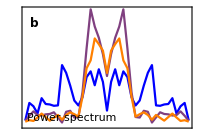

```mathematica
plotPspecNorm=ListLinePlot[specNormData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.5cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+4*heightEws+heightBif+4*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotAc1,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxAc1,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotSmaxVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSmaxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotCv,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxCv,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th (top) row  *)
Inset[Show[plotTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspecNorm,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

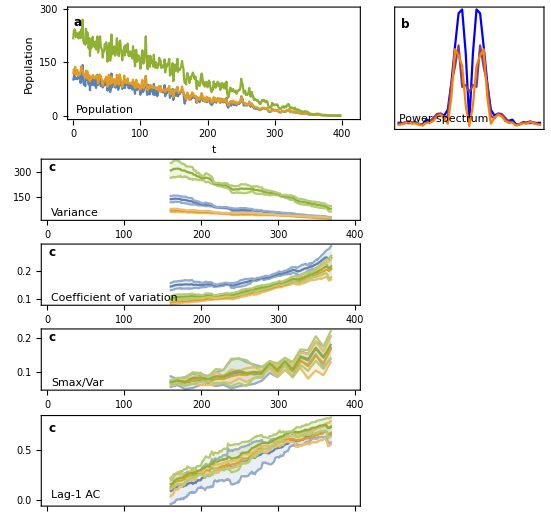

```mathematica
plotGrid
```

```mathematica
(*Export["figures/intervals_"<>simName<>".png",plotGrid,ImageResolution->100];*)
```